```mathematica
Quit[]
```

```mathematica
(* Package for plotting with LaTeX fonts *)
<<MaTeX`
```

## Fitting Functions

### Genetic Algorithm

```mathematica
a1=101.855;
a2=21112.189;
a3=35913.065;
a4=1428.081;
a5=1.03922;
a6=1.36418;
a7=0.78991;
a8=0.5426;
a9=0.7349;
a10=0.10047;
a11=0.1485;
a12=0.0005236;
a13=49.99978;
a14=46.02641;
a15=1.0049;
b1=1.483;
b2=3.972;
b3=6.097;
b4=7.507;
b5=2.7345;
b6=0.9914;
b7=0.26955;
b8=1.19806;
b9=0.739668;
b10=0.76324;
b11=1.49987;
b12=1.47345;
b13=0.96164;
b14=1.24458;
b15=0.234948;

c1=0.00785436;
c2=0.177084;
c3=0.00912388;
c4=0.618711;
c5=11.9611;
c6=2.81343;
c7=0.784719;

AS1=0.006249;
kS1=0.199435;
σS1=0.062686;
AS2=0.00837;
kS2=0.081;
σS2=0.0404;
AS3=0.012538;
kS3=0.14376;
σS3=0.007586;
AS4=0.0038985;
kS4=1.1791;
σS4=0.3;

q[k_,h_,ωb_,ωm_]:=(h*k)/(ωm-ωb)
Tnw[k_,h_,ωb_,ωm_]:=(1+a1*q[k,h,ωb,ωm]^b1+a2*q[k,h,ωb,ωm]^b2+ a3*q[k,h,ωb,ωm]^b3+a4*q[k,h,ωb,ωm]^b4)^(-1/4)

fα[ωb_,ωm_]:=a10-a11*ωb^b10+a12*ωm^b11
fβ[ωb_,ωm_]:=b12-a13*ωb^b13+a14*ωm^b14
fnode[ωm_]:=a15*ωm^b15 
sGA[ωb_,ωm_]:=1/(c1*ωb^c2+c3*ωm^c4+c5*ωb^c6*ωm^c7)
kSilk[ωb_,ωm_]:=0.373 ωb^0.419+0.195 ωm^1.0957
Tw[k_,h_,ωb_,ωm_]:=1+fα[ωb,ωm]/(a5+(fβ[ωb,ωm]/(k*h*sGA[ωb,ωm]))^b5)*ⅇ^(-a6(k*h/kSilk[ωb,ωm])^b6)*Sin[a7(k*h*sGA[ωb,ωm]+a8*ωm^-b7)/((a9+(fnode[ωm]/(k*h*sGA[ωb,ωm]))^b8)^b9)]
TS1[k_]:=1-AS1*ⅇ^(-((k-kS1)/σS1)^2)
TGA[k_,h_,ωb_,ωm_]:=Tnw[k,h,ωb,ωm]*Tw[k,h,ωb,ωm]*TS1[k]

PS2[k_]:=1+AS2*ⅇ^(-((k-kS2)/σS2)^2)
PS3[k_]:=1-AS3*ⅇ^(-((k-kS3)/σS3)^2)
PS4[k_]:=1-AS4*ⅇ^(-((k-kS4)/σS4)^2)

PGA[k_,h_,ωb_,ωm_,ns_,A0_]:=A0*k^ns*TGA[k,h,ωb,ωm]^2*PS2[k]*PS3[k]*PS4[k]

keq[h_,ωb_,ωm_,ns_]:=(0.07066 ns^0.939 ωm^0.8824)/(h^1.00649 (1+1.2025 ωb)^3.3395)
Pkeq[h_,ωb_,ωm_,ns_,As_]:=(7080.944 As ⅇ^(-1.2303 ωb) h^2.081426)/(ns^1.49408 ωm^0.66927)
Req[h_,ωb_,ωm_,ns_]:=0.6461-0.0097 h^2+0.0307ns+7.1728ωb+0.0239/ωm
PGAeq[h_,ωb_,ωm_,ns_]:=(0.04682 ⅇ^(-8.611 ωb) ωm^1.0587)/(h^0.8998 ns^3.916)
DPGAeq[h_,ωb_,ωm_,ns_]:=-0.38598+0.005318h-0.00145 h^2+0.2277ns-0.086155 ns^2-1.86 ωb-28.6088 ωb^2+2.9997ωm-6.426 ωm^2
B[h_,ωb_,ωm_,ns_]:=Req[h,ωb,ωm,ns]-1
A[h_,ωb_,ωm_,ns_,σ_,λ_]:=-(DPGAeq[h,ωb,ωm,ns]/PGAeq[h,ωb,ωm,ns])(1+B[h,ωb,ωm,ns])-√(2/π)(λ/σ)B[h,ωb,ωm,ns]
Pc[k_,h_,ωb_,ωm_,ns_,σ_,λ_]:=1+(A[h,ωb,ωm,ns,σ,λ](k-keq[h,ωb,ωm,ns])+B[h,ωb,ωm,ns])ⅇ^(-1/2(k-keq[h,ωb,ωm,ns])^2/σ^2)(1+Erf[λ*(k-keq[h,ωb,ωm,ns])/(√2 σ)])
```

### Eisenstein-Hu: No-Wiggles

```mathematica
Θ=Solve[2.7*x==2.728]⟦1,1,2⟧;  (* Tcmb = 2.7Θ = 2.728 -> By FIRAS *)
sEH[ωb_,ωm_]:=(44.5*Log[9.83/ωm])/(√(1+10 ωb^(3/4))); (* Mpc *)
αΓ[ωb_,ωm_]:=1-0.328*Log[431*ωm]*ωb/ωm+0.38*Log[22.3*ωm]*(ωb/ωm)^2
Γeff[k_,h_,ωb_,ωm_]:=ωm/h(αΓ[ωb,ωm]+(1-αΓ[ωb,ωm])/(1+(0.43*k*sEH[ωb,ωm])^4));
qeff[k_,h_,ωb_,ωm_]:=k/h*Θ^2/Γeff[k,h,ωb,ωm]; (* k in h/Mpc *)
L0eff[k_,h_,ωb_,ωm_]:=Log[2ⅇ+1.8*qeff[k,h,ωb,ωm]];
C0eff[k_,h_,ωb_,ωm_]:=14.2+731/(1+62.5*qeff[k,h,ωb,ωm]);
TEHnw[k_,h_,ωb_,ωm_]:=L0eff[k,h,ωb,ωm]/(L0eff[k,h,ωb,ωm]+C0eff[k,h,ωb,ωm]*qeff[k,h,ωb,ωm]^2)
PEHnw[k_,h_,ωb_,ωm_,ns_,A0_]:=A0*k^ns*TEHnw[k*h,h,ωb,ωm]^2
```

### Eisenstein-Hu

```mathematica
(* All the formulas are extracted from EH97I[9709112 v1] paper,unless stated. *)
Θ=Solve[2.7*x==2.728]⟦1,1,2⟧;  (* Tcmb = 2.7Θ = 2.728 -> By FIRAS *)
(* See Eq. (11) *)
a1EH[ωm_]:=(46.9ωm)^0.670 (1+(32.1 ωm)^-0.532)
a2EH[ωm_]:=(12.0 ωm)^0.424 (1+(45.0 ωm)^-0.582) 
αc[ωb_,ωm_]:=a1EH[ωm]^(-ωb/ωm)*a2EH[ωm]^(-(ωb/ωm)^3)
(* See Eq. (12) *)
b1EH[ωm_] := 0.944 (1+(458 ωm)^-0.708)^-1 
b2EH[ωm_]:=(0.395 ωm)^-0.0266 
βc[ωb_,ωm_]:=(1+b1EH[ωm](((ωm - ωb)/ωm)^b2EH[ωm]-1))^-1 
(* Redshift at drag epoch -> See Eq. (4) *)
b1d[ωm_]:=0.313 ωm^-0.419 (1 + 0.607 ωm^0.674) 
b2d[ωm_]:=0.238 ωm^0.223 
zd[ωb_,ωm_]:=1291*ωm^0.251/(1 + 0.659 ωm^0.828)(1 + b1d[ωm] ωb^b2d[ωm]) 
zeqEH[ωm_]:=2.5*10^4 ωm*Θ^-4 (* Redshift at equilibrium epoch -> See Eq. (2) *)
keqEH[ωm_]:=7.46*10^-2 ωm*Θ^-2  (* scale at equilibrium epoch -> See Eq. (3) *)
qEH[k_,ωm_] := k/(13.41 keqEH[ωm])  (* See Eq. (10) *)
REH[z_,ωb_]:=31.5*ωb*Θ^-4*(z/10^3)^-1  (* Baryon-Photon ratio -> See Eq. (5) *)
yEH[z_,ωm_]:=(1+zeqEH[ωm])/(1+z) (* Useful variable for calculations in LS limit -> See Eq.(8.20) in Dodelson 2 *)
(* Sub-horizon solution of the Mezsaros' eq. -> See Eq. (8.63) in Dodelson 2 *)
GEH[z_,ωm_]:=yEH[z, ωm] (-6 √(1+yEH[z,ωm])+(2+3yEH[z,ωm])Log[(√(1 + yEH[z, ωm])+1)/(√(1 + yEH[z, ωm])-1)]) 
(* Silk damping scale -> See Eq. (7) *)
kSilkEH[ωb_,ωm_]:=1.6 ωb^0.52*ωm^0.73(1+(10.4 ωm)^-0.95) (* [(Mpc^-1)]*)
βnode[ωm_]:=8.41*ωm^0.435 (* Shifting of nodes parameter -> See Eq. (23) *)
st[k_,ωb_,ωm_]:=sEH[ωb,ωm]/((1+(βnode[ωm]/(k*sEH[ωb, ωm]))^3)^(1/3)) (* Shifting of oscillations nodes -> See Eq. (22) *)
(* Amplitude of small scale contributions -> See Eq. (14) *)
αb[ωb_,ωm_]:=2.07*keqEH[ωm]*sEH[ωb,ωm] (1+REH[zd[ωb,ωm],ωb])^(-3/4)GEH[yEH[zd[ωb,ωm],ωm], ωm] 

(* Small scale contributions -> See Eq. (24) *)
βb[ωb_,ωm_]:=0.5+ωb/ωm+(3-2 ωb/ωm) √((17.2 ωm)^2+1)
fEH[k_,ωb_,ωm_]:=1/(1 + ((k*sEH[ωb, ωm])/5.4)^4) (* See Eq (18) *)
Cf[k_,ωb_,ωm_]:=14.2/αc[ωb,ωm]+386/(1 + 69.9*qEH[k,ωm]^1.08) (* See Eq. (20) *)
Cfαc1[k_,ωb_,ωm_]:=14.2 + 386/(1 + 69.9*qEH[k,ωm]^1.08) (* Cf with αc = 1*)
(* See Eq. (19) *)
T0[k_,ωb_,ωm_]:=Log[ⅇ + 1.8*βc[ωb,ωm]*qEH[k,ωm]]/(Log[ⅇ+1.8 βc[ωb,ωm]*qEH[k,ωm]]+Cf[k,ωb,ωm]*qEH[k,ωm]^2)
(* See Eqs. (19) and (20) in EH97: T0(k, 1, βc) means αc = 1 in Eq. (20) *)
T01[k_,ωb_,ωm_]:=Log[ⅇ+1.8*βc[ωb,ωm]*qEH[k,ωm]]/(Log[ⅇ + 1.8 βc[ωb,ωm]*qEH[k,ωm]]+Cfαc1[k,ωb,ωm]*qEH[k,ωm]^2)
(* See Eq. (19) in EH97: T0(k, 1, 1) means αc = 1 in Eq. (20) and βc = 1 in Eq. (19) *)
T011[k_,ωb_,ωm_]:=Log[ⅇ+1.8*qEH[k,ωm]]/(Log[ⅇ+1.8*qEH[k,ωm]]+Cfαc1[k,ωb,ωm]*qEH[k,ωm]^2)
(* Transfer function for CDM -> See Eq. (17) *)
TcEH[k_,ωb_,ωm_]:=fEH[k,ωb,ωm]*T01[k,ωb,ωm]+(1-fEH[k,ωb,ωm])T0[k,ωb,ωm]
(* Transfer function for baryons -> See Eq. (21) *)
TbEH[k_,ωb_,ωm_]:=(T011[k, ωb, ωm]/(1+((k*sEH[ωb,ωm])/5.2)^2)+αb[ωb,ωm]/(1 + (βb[ωb,ωm]/(k*sEH[ωb,ωm]))^3)ⅇ^(-(k/kSilkEH[ωb,ωm])^1.4))Sin[k*st[k,ωb,ωm]]/(k*st[k,ωb,ωm])
(* Transfer function for CDM + baryons -> See Eq. (16) *)
TEH[k_,ωb_,ωm_] := (ωm - ωb)/ωm TcEH[k,ωb,ωm]+ωb/ωm TbEH[k,ωb,ωm]
PEH[k_,h_,ωb_,ωm_,ns_,A0_]:=A0*k^ns*TEH[k*h,ωb,ωm]^2
```

### Operon

```mathematica
b0B=0.0545;
b1B=0.0038;
b2B=0.0397;
b3B=0.1277;
b4B=1.35;
b5B=4.0535;
b6B=0.0008;
b7B=1.8852;
b8B=0.1142;
b9B=3.798;
b10B=14.909;
b11B=5.56;
b12B=15.8274;
b13B=0.0231;
b14B=0.8653;
b15B=0.8425;
b16B=4.554;
b17B=5.117;
b18B=70.0234;
b19B=0.0111;
b20B=5.35;
b21B=6.421;
b22B=134.309;
b23B=5.324;
b24B=21.532;
b25B=4.742;
b26B=16.6872;
b27B=3.078;
b28B=16.987;
b29B=0.0588;
b30B=0.0007;
b31B=195.498;
b32B=0.0038;
b33B=0.2767;
b34B=7.385;
b35B=12.3961;
b36B=0.0134;

logF[k_,h_,Ωb_,Ωm_]:=b0B*h-b1B+((b2B*Ωb)/(√(h^2+b3B)))^(b4B*Ωm)((b5B*k-Ωb)/(√(b6B+(Ωb-b7B*k)^2))*b8B*(b9B*k)^(-b10B*k)Cos[b11B*Ωm-(b12B*k)/(√(b13B+Ωb^2))]-b14B*((b15B*k)/(√(1+b16B*k^2))-Ωm)*Cos[(b17B*h)/(√(1+b18B*k^2))])+b19B*(b20B*Ωm+b21B*h-Log[b22B*k]+(b23B*k)^(-b24B*k))*Cos[b25B/(√(1+b26B*k^2))]+(b27B*k)^(-b28B*k)(b29B*k-(b30B*Log[b31B*k])/(√(b32B+(Ωm-b33B*h)^2)))Cos[b34B*Ωm-(b35B*k)/(√(b36B+Ωb^2))]
FB[k_,h_,Ωb_,Ωm_]:=Exp[logF[k,h,Ωb,Ωm]]
```

#### Correction

```mathematica
e0B=0.2841;
e1B=0.1679;
e4B=0.1183;
e5B=0.3971;
e9B=0.2476;
e10B=0.1841;
e12B=0.1385;
e13B=0.2825;
e15B=0.019;
e16B=0.1376;
e17B=0.3733;
log10SB[k_,h_,Ωb_,Ωm_]:=1/10(-e0B*h+e1B-e4B/e5B+(e9B*Ωb+e10B+e12B-e13B)/(√(e15B+(Ωm+e16B*Log[e17B])^2)))
SB[k_,h_,Ωb_,Ωm_]:=10^log10SB[k,h,Ωb,Ωm]
```

```mathematica
sB[h_,Ωb_,Ωm_]:=(44.5*Log[9.83/(Ωm*h^2)])/(√(1.0+10.0(Ωb*h^2)^(3/4)))
αB[h_,Ωb_,Ωm_]:=1.0-0.328*Log[431.0*(Ωm*h^2)]*(Ωb*h^2)+0.38*Log[22.3*(Ωm*h^2)]*(Ωb*h^2)^2
ΓB[k_,h_,Ωb_,Ωm_]:=Ωm*h(αB[h,Ωb,Ωm]+(1.0-αB[h,Ωb,Ωm])/(1.0+(0.43*k*h*sB[h,Ωb,Ωm])^4))
qB[k_,h_,Ωb_,Ωm_]:=k*2.7255/2.7*ΓB[k,h,Ωb,Ωm]^-1
C0B[k_,h_,Ωb_,Ωm_]:=14.2+731.0/(1+62.5*qB[k,h,Ωb,Ωm])
L0B[k_,h_,Ωb_,Ωm_]:=Log[2*ⅇ+1.8qB[k,h,Ωb,Ωm]]
kpivot=0.05; (* h/Mpc *)
c=2998;
PEHB[k_,h_,Ωb_,Ωm_,ns_,As_]:=(2 π^2)/k^3*As*10^-9*(k/kpivot)^(ns-1)((2 k^2 c^2)/(5Ωm)*L0B[k,h,Ωb,Ωm]/(L0B[k,h,Ωb,Ωm]+C0B[k,h,Ωb,Ωm]*qB[k,h,Ωb,Ωm]^2))^2
```

```mathematica
PΛCDMB[k_,h_,Ωb_,Ωm_,ns_,As_]:=PEHB[k,h,Ωb,Ωm,ns,As]*FB[k,h,Ωb,Ωm]
PkB[k_,h_,Ωb_,Ωm_,ns_,As_]:=SB[k,h,Ωb,Ωm]*PΛCDMB[k,h,Ωb,Ωm,ns,As]
```

## Planck

### Data

```mathematica
(* Data from CLASS *)
PlanckData=Import["./Data/planck_pk.dat","Table"][[5;;-1]];
PlanckPk=Interpolation[PlanckData];
```

```mathematica
hPlanck=0.6766;
ωbPlanck=0.02242;
ΩbPlanck=ωbPlanck*hPlanck^-2;
ωmPlanck=0.1424;
ΩmPlanck=0.3111;
nsPlanck=0.9665;
AsPlanck=2.105;
σ8Planck=0.8102;
```

### Compute Normalization

```mathematica
R8=8;            (*radio en Mpc/h*)
(*Función ventana top-hat*)
WtopHat[x_]:=3/x^3(Sin[x]-x Cos[x]);
IntegralEH=NIntegrate[k^(nsPlanck+2) TEHnw[k*hPlanck,hPlanck,ωbPlanck,ωmPlanck]^2(WtopHat[R8*k])^2,{k,10^-5,10},Method->{"GlobalAdaptive"},MaxRecursion->15,AccuracyGoal->6];
A0EH=2*π^2 σ8Planck^2/IntegralEH;
IntegralGA:=NIntegrate[k^(nsPlanck+2) Tnw[k,hPlanck,ωbPlanck,ωmPlanck]^2(WtopHat[R8*k])^2,{k,10^-5,2},Method->{"GlobalAdaptive"},MaxRecursion->15,AccuracyGoal->6];
A0GA=2*π^2 σ8Planck^2/IntegralGA;
```

### Compute Correction

```mathematica
(* Formula for (d^2 Subscript[P, class])/dk^2 at Subscript[k, eq] *)
DDPkclass[h_,ωb_,ωm_,ns_,As_]:=-10^((ωb+10.904067-Cos[h]-(1.1083639/(h+3 ωb)+Log[ns]+6.28427 ωm+ωm))+0.43375605 Log[As]) 
λGA=0.4;
```

```mathematica
(* Compute (d^2 Subscript[P, GA])/dk^2 at Subscript[k, eq] and solve for σ by equaling to (d^2 Subscript[P, class])/dk^2 at Subscript[k, eq] *)
(* Fix λ = 0.4 *)
DDP=D[D[PGA[k,hPlanck,ωbPlanck,ωmPlanck,nsPlanck,A0GA]*Pc[k,hPlanck,ωbPlanck,ωmPlanck,nsPlanck,σ,λGA],k],k]/.k->keq[hPlanck,ωbPlanck,ωmPlanck,nsPlanck]//Simplify;
σDDP=Solve[DDP==DDPkclass[hPlanck,ωbPlanck,ωmPlanck,nsPlanck,AsPlanck],σ]//Quiet
```

{{σ→-0.00130173},{σ→-0.000107481}}

```mathematica
σGA=Re[σDDP[[2,1,2]]]
```

-0.000107481

### Accuracy

#### Genetic Algorithm

```mathematica
AccGA=Table[{PlanckData[[j,1]],Abs[1-PGA[PlanckData[[j,1]],hPlanck,ωbPlanck,ωmPlanck,nsPlanck,A0GA]/PlanckData[[j,2]]*Pc[PlanckData[[j,1]],hPlanck,ωbPlanck,ωmPlanck,nsPlanck,σGA,λGA]]*100},{j,1,Length[PlanckData]}];//Quiet
%[[All,2]][[31;;-1]]//Mean
```

0.331983

#### Eisenstein-Hu

```mathematica
AccEH=Table[{PlanckData[[j,1]],Abs[1-PEH[PlanckData[[j,1]],hPlanck,ωbPlanck,ωmPlanck,nsPlanck,A0EH]/PlanckData[[j,2]]]*100},{j,1,Length[PlanckData]}];//Quiet
%[[All,2]][[31;;-1]]//Mean
```

2.17392

#### Operon

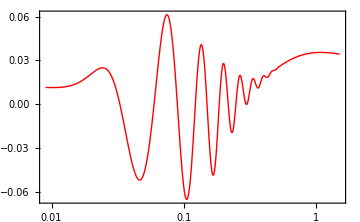

```mathematica
LogLinearPlot[logF[k,hPlanck,ΩbPlanck,ΩmPlanck],{k,9*10^-3,1.5},PlotRange->All,PlotStyle->{Directive[Red,Thick],Directive[Red,Thick]},Frame->True,FrameStyle->BlackFrame,FrameLabel->(MaTeX[#,Magnification->1.4]&)/@{"k~[h / \\text{Mpc}]","\\text{log}~F"},BaseStyle->{FontFamily->"Times",FontSize->14},ImageSize->Medium]//Quiet
```

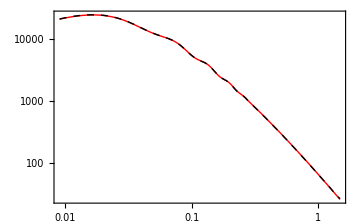

```mathematica
LogLogPlot[{PEHnw[k,hPlanck,ωbPlanck,ωmPlanck,nsPlanck,A0EH]*FB[k,hPlanck,ΩbPlanck,ΩmPlanck],PlanckPk[k]},{k,9*10^-3,1.5},PlotRange->All,PlotStyle->{Directive[Red,Thick],Directive[Black,Thick,Dashed]},Frame->True,FrameStyle->BlackFrame,FrameLabel->(MaTeX[#,Magnification->1.4]&)/@{"k~[h / \\text{Mpc}]","P(k)~[(\\text{Mpc}/h)^3]"},BaseStyle->{FontFamily->"Times",FontSize->14},ImageSize->Medium]//Quiet
```

```mathematica
AccBI=Table[{PlanckData[[j,1]],Abs[1-FB[PlanckData[[j,1]],hPlanck,ΩbPlanck,ΩmPlanck]/PlanckData[[j,2]] PEHnw[PlanckData[[j,1]],hPlanck,ωbPlanck,ωmPlanck,nsPlanck,A0EH]]*100},{j,1,Length[PlanckData]}];//Quiet
%[[All,2]][[31;;-1]]//Mean
```

0.226804

### Comparison

```mathematica
{LeafCount[#],Depth[#]}&@(FB[k,h,Ωb,Ωm]*PEHnw[k,h,ωb,ωm,ns,A0]*SB[k,h,Ωb,Ωm])
{LeafCount[#],Depth[#]}&@(PGA[k,h,ωb,ωm,ns,A0]*Pc[k,h,ωb,ωm,ns,σ,λ])
```

{616,20}

{482,15}

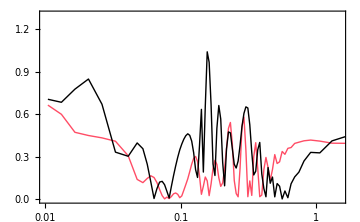

```mathematica
ListLogLinearPlot[{AccBI[[31;;-1]],AccGA[[31;;-1]]},Joined->True,PlotRange->{{0.01,1.5},{0,1.3}},PlotStyle->{Directive[RGBColor[1,0.3,0.4],Thick],Directive[Black,Thick]},Frame->True,FrameStyle->BlackFrame,FrameLabel->(MaTeX[#,Magnification->1.4]&)/@{"k~[h / \\text{Mpc}]","\\text{Acc}"},BaseStyle->{FontFamily->"Times",FontSize->16},PlotLegends->Placed[LineLegend[{(MaTeX[#,Magnification->1.2]&)/@Style["\\text{Ce Sui et al}"],Style[MaTeX["\\text{GA}",Magnification->1.2]]},LegendLayout->{"Row",2},LabelStyle->{Black,Bold,5},LegendFunction->"Frame",LegendMarkerSize->{30,15}],{0.22,0.815}],ImageSize->Medium]//Quiet
```

## Fiducial

### Data

```mathematica
(* Data from CLASS *)
FidData=Import["./Data/fiducial_pk.dat","Table"][[5;;-1]];
```

```mathematica
a0B=0.51172;
a1B=0.04593;
a2B=0.73983;
a3B=1.56738;
a4B=1.16846;
a5B=0.59348;
a6B=0.19994;
a7B=25.09218;
a8B=9.36909;
a9B=0.00011;
σ8B[h_,Ωb_,Ωm_,ns_,As_]:=√As*(a0B*Ωm+a1B*h+a2B(Ωm-a3B*Ωb)(Log[a4B*Ωm]-a5B*ns)*(ns+a6B*h(a7B*Ωb-a8B*ns+Log[a9B*h])))
AsB[h_,Ωb_,Ωm_,ns_,σ8_]:=σ8^2*(a0B*Ωm+a1B*h+a2B(Ωm-a3B*Ωb)(Log[a4B*Ωm]-a5B*ns)*(ns+a6B*h(a7B*Ωb-a8B*ns+Log[a9B*h])))^-2
```

```mathematica
(* Parameters from Quijote *)
hFid=0.6711;
ΩbFid=0.049;
ωbFid=ΩbFid*hFid^2;
ΩmFid=0.3175;
ωmFid=ΩmFid*hFid^2;
nsFid=0.9624;
σ8Fid=0.834;
AsFid=AsB[hFid,ΩbFid,ΩmFid,nsFid,σ8Fid];(* Corresponding Subscript[A, s] *)
```

### Compute Normalization

```mathematica
R8=8;            (*radio en Mpc/h*)
(*Función ventana top-hat*)
WtopHat[x_]:=3/x^3(Sin[x]-x Cos[x]);
IntegralEH=NIntegrate[k^(nsFid+2) TEHnw[k*hFid,hFid,ωbFid,ωmFid]^2(WtopHat[R8*k])^2,{k,10^-5,10},Method->{"GlobalAdaptive"},MaxRecursion->15,AccuracyGoal->6];
A0EH=2*π^2 σ8Fid^2/IntegralEH;
IntegralGA:=NIntegrate[k^(nsFid+2) Tnw[k,hFid,ωbFid,ωmFid]^2(WtopHat[R8*k])^2,{k,10^-5,2},Method->{"GlobalAdaptive"},MaxRecursion->15,AccuracyGoal->6];
A0GA=2*π^2 σ8Fid^2/IntegralGA;
```

### Compute Correction

```mathematica
(* Formula for (d^2 Subscript[P, class])/dk^2 at Subscript[k, eq] *)
DDPkclass[h_,ωb_,ωm_,ns_,As_]:=-10^((ωb+10.904067-Cos[h]-(1.1083639/(h+3 ωb)+Log[ns]+6.28427 ωm+ωm))+0.43375605 Log[As]) 
λGA=0.4;
(* Compute (d^2 Subscript[P, GA])/dk^2 at Subscript[k, eq] and solve for σ by equaling to (d^2 Subscript[P, class])/dk^2 at Subscript[k, eq] *)
(* Fix λ = 0.4 *)
DDP=D[D[PGA[k,hFid,ωbFid,ωmFid,nsFid,A0GA]*Pc[k,hFid,ωbFid,ωmFid,nsFid,σ,λGA],k],k]/.k->keq[hFid,ωbFid,ωmFid,nsFid]//Simplify;
σDDP=Solve[DDP==DDPkclass[hFid,ωbFid,ωmFid,nsFid,AsFid],σ]//Quiet
```

{{σ→-0.0116892},{σ→0.0158978}}

```mathematica
σGA=Re[σDDP[[1,1,2]]];
```

### Accuracy

#### Genetic Algorithm

```mathematica
AccGA=Table[{FidData[[j,1]],Abs[1-PGA[FidData[[j,1]],hFid,ωbFid,ωmFid,nsFid,A0GA]/FidData[[j,2]]*Pc[FidData[[j,1]],hFid,ωbFid,ωmFid,nsFid,σGA,λGA]]*100},{j,1,Length[FidData]}];//Quiet
%[[All,2]][[31;;-1]]//Mean
```

0.319598

#### Eisenstein-Hu

```mathematica
AccEH=Table[{FidData[[j,1]],Abs[1-PEH[FidData[[j,1]],hFid,ωbFid,ωmFid,nsFid,A0EH]/FidData[[j,2]]]*100},{j,1,Length[FidData]}];//Quiet
%[[All,2]][[31;;-1]]//Mean
```

2.18605

#### Operon

```mathematica
AccBI=Table[{FidData[[j,1]],Abs[1-FB[FidData[[j,1]],hFid,ΩbFid,ΩmFid]/FidData[[j,2]] PEHnw[FidData[[j,1]],hFid,ωbFid,ωmFid,nsFid,A0EH]]*100},{j,1,Length[FidData]}];//Quiet
%[[All,2]][[31;;-1]]//Mean
```

0.163745

### Comparison

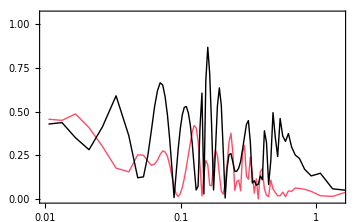

```mathematica
ListLogLinearPlot[{AccBI[[31;;-1]],AccGA[[31;;-1]]},Joined->True,PlotRange->{{0.01,1.5},{0,1.05}},PlotStyle->{Directive[RGBColor[1,0.3,0.4],Thick],Directive[Black,Thick]},Frame->True,FrameStyle->BlackFrame,FrameLabel->(MaTeX[#,Magnification->1.4]&)/@{"k~[h / \\text{Mpc}]","\\text{Acc}"},BaseStyle->{FontFamily->"Times",FontSize->16},PlotLegends->Placed[LineLegend[{(MaTeX[#,Magnification->1.2]&)/@Style["\\text{Ce Sui et al}"],Style[MaTeX["\\text{GA}",Magnification->1.2]]},LegendLayout->{"Row",2},LabelStyle->{Black,Bold,5},LegendFunction->"Frame",LegendMarkerSize->{30,15}],{0.22,0.815}],ImageSize->Medium]//Quiet
```

## Latin HyperCube

```mathematica
Quit[]
```

### Packages

```mathematica
SetDirectory[NotebookDirectory[]];
<<MaTeX` (* Package to make plots with LaTeX fonts *)
LaunchKernels[];
Off[General::munfl];
Off[General::stop];
Off[Infinity::indet];
Off[Power::infy];
Off[Indeterminate::indet];
```

### Data

```mathematica
Import["./Data/cosmo_params_syren_new.txt","Table"][[1]]
Params=Import["./Data/cosmo_params_syren_new.txt","Table"][[2;;-1]];
```

{h,omega_b,omega_m,ns,10^9As,sigma8}

```mathematica
dir="./Data/spectra_syren_new/";
paths=FileNameJoin[{dir,"spectrum_"<>IntegerString[#,10,3]<>".txt"}]&/@Range[1,Length[Params]];
PkData=Rest[Import[#,"Data"]]&/@paths;
```

### Compute Normalization

```mathematica
R8=8;            (*radio en Mpc/h*)
(*Función ventana top-hat*)
WtopHat[x_]:=3/x^3(Sin[x]-x Cos[x]);
σ8=Params[[All,6]];
IntegralGA[i_]:=NIntegrate[k^(Params[[i,4]]+2) Tnw[k,Params[[i,1]],Params[[i,2]],Params[[i,3]]]^2(WtopHat[R8*k])^2,{k,10^-5,2},Method->{"GlobalAdaptive"},MaxRecursion->15,AccuracyGoal->6];
A0GA=ParallelTable[2*π^2 σ8[[i]]^2/IntegralGA[i],{i,1,Length[Params]}];
IntegralEH[i_]:=NIntegrate[k^(Params[[i,4]]+2) TEHnw[k*Params[[i,1]],Params[[i,1]],Params[[i,2]],Params[[i,3]]]^2(WtopHat[R8*k])^2,{k,10^-5,2},Method->{"GlobalAdaptive"},MaxRecursion->15,AccuracyGoal->6];
A0EH=ParallelTable[2*π^2 σ8[[i]]^2/IntegralEH[i],{i,1,Length[Params]}];
```

### Compute Correction

```mathematica
(* Formula for (d^2 Subscript[P, class])/dk^2 at Subscript[k, eq] *)
DDPkclass[h_,ωb_,ωm_,ns_,As_]:=-10^((ωb+10.904067-Cos[h]-(1.1083639/(h+3 ωb)+Log[ns]+6.28427 ωm+ωm))+0.43375605 Log[As]) 
λFixed=0.4;
(* Compute (d^2 Subscript[P, GA])/dk^2 at Subscript[k, eq] and solve for σ by equaling to (d^2 Subscript[P, class])/dk^2 at Subscript[k, eq] *)
(* Fix λ = 0.4 *)
DDP=Table[D[D[PGA[k,Params[[i,1]],Params[[i,2]],Params[[i,3]],Params[[i,4]],A0GA[[i]]]*Pc[k,Params[[i,1]],Params[[i,2]],Params[[i,3]],Params[[i,4]],σ,λFixed],k],k]/.k->keq[Params[[i,1]],Params[[i,2]],Params[[i,3]],Params[[i,4]]],{i,1,Length[Params]}]//Simplify;
σDDP=Table[Solve[DDP[[i]]==DDPkclass[Params[[i,1]],Params[[i,2]],Params[[i,3]],Params[[i,4]],Params[[i,5]]],σ]//Quiet,{i,Length[Params]}];
(* Take the smallest one in absolute value *)
MinAbsKeepSign[pair_]:=First@MinimalBy[pair,Abs]
σFullGA=MinAbsKeepSign/@Table[{Re[σDDP[[i]][[1,1,2]]],Re[σDDP[[i]][[2,1,2]]]},{i,1,Length[Params]}];
```

### Accuracy

#### Genetic Algorithm

```mathematica
AccGA[i_]:=Table[{PkData[[i]][[j,1]],Abs[1-(PGA[PkData[[i]][[j,1]],Params[[i,1]],Params[[i,2]],Params[[i,3]],Params[[i,4]],A0GA[[i]]]*Pc[PkData[[i]][[j,1]],Params[[i,1]],Params[[i,2]],Params[[i,3]],Params[[i,4]],σFullGA[[i]],λFixed])/PkData[[i]][[j,2]]]*100},{j,1,Length[PkData[[i]]]}]
```

```mathematica
{Mean[#],Min[#],Max[#],Position[#,Min[#]],Position[#,Max[#]]}&@Table[Mean[AccGA[i][[All,2]][[95;;-1]]],{i,1,Length[Params]}]//Quiet
WorstFitGA=Position[#,Max[#]][[1,1]]&@Table[Mean[AccGA[i][[All,2]][[95;;-1]]],{i,1,Length[Params]}]//Quiet;
BestFitGA=Position[#,Min[#]][[1,1]]&@Table[Mean[AccGA[i][[All,2]][[95;;-1]]],{i,1,Length[Params]}]//Quiet;
```

{0.294837,0.164963,0.623752,{{37}},{{134}}}

#### Eisenstein-Hu

```mathematica
AccEH[i_]:=Table[{PkData[[i]][[j,1]],100*Abs[1-A0EH[[i]]/(PkData[[i]][[j,2]])*(PkData[[i]][[j,1]])^Params[[i,4]]*TEH[PkData[[i]][[j,1]]*Params[[i,1]],Params[[i,2]],Params[[i,3]]]^2]},{j,Length[PkData[[i]]]}];
```

```mathematica
{Mean[#],Min[#],Max[#],Position[#,Min[#]],Position[#,Max[#]]}&@Table[Mean[AccEH[i][[All,2]][[95;;-1]]],{i,1,Length[Params]}]//Quiet
WorstFitEH=Position[#,Max[#]][[1,1]]&@Table[Mean[AccEH[i][[All,2]][[95;;-1]]],{i,1,Length[Params]}]//Quiet;
BestFitEH=Position[#,Min[#]][[1,1]]&@Table[Mean[AccEH[i][[All,2]][[95;;-1]]],{i,1,Length[Params]}]//Quiet;
```

{2.1733,2.11207,2.23368,{{16}},{{151}}}

#### Operon

```mathematica
AccB[i_]:=Table[{PkData[[i]][[j,1]],100*Abs[1-FB[PkData[[i]][[j,1]],Params[[i,1]],Params[[i,2]]/Params[[i,1]]^2,Params[[i,3]]/Params[[i,1]]^2]/(PkData[[i]][[j,2]])*PEHnw[PkData[[i]][[j,1]],Params[[i,1]],Params[[i,2]],Params[[i,3]],Params[[i,4]],A0EH[[i]]]]},{j,Length[PkData[[i]]]}];
```

```mathematica
{Mean[#],Min[#],Max[#],Position[#,Min[#]],Position[#,Max[#]]}&@Table[Mean[AccB[i][[All,2]][[95;;-1]]],{i,1,Length[Params]}]//Quiet
WorstFitB=Position[#,Max[#]][[1,1]]&@Table[Mean[AccB[i][[All,2]][[95;;-1]]],{i,1,Length[Params]}]//Quiet;
BestFitB=Position[#,Min[#]][[1,1]]&@Table[Mean[AccB[i][[All,2]][[95;;-1]]],{i,1,Length[Params]}]//Quiet;
```

{0.255462,0.152768,0.610367,{{83}},{{174}}}

### Comparison

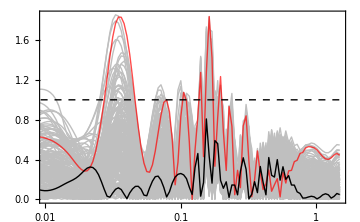

```mathematica
Module[{curves,styles,legendLabels},curves=Join[Table[AccGA[i],{i,Select[Range[Length[Params]],#!=BestFitGA&&#!=WorstFitGA&]}],{AccGA[WorstFitGA],AccGA[BestFitGA]}];
styles=Join[Table[Directive[Thin,GrayLevel[0.75]],{Length[Params]-2}],{Directive[Thick,Red,Opacity[0.7]](*Worst fit*),
Directive[Thick,Black](*Best fit*)}];
legendLabels={(MaTeX[#,Magnification->1.2]&)/@Style["\\text{Worst fit}"],(MaTeX[#,Magnification->1.2]&)/@Style["\\text{Best fit}"]};
ListLogLinearPlot[curves,Joined->True,PlotRange->{{10^-2,1.5},All},PlotStyle->styles,Frame->True,FrameStyle->BlackFrame,FrameLabel->(MaTeX[#,Magnification->1.4]&)/@{"k~[h / \\text{Mpc}]","\\text{Acc}(\\text{GA})"},BaseStyle->{FontFamily->"Times",FontSize->16},PlotLegends->Placed[LineLegend[styles[[-2;;]],legendLabels,LegendLayout->{"Row",3},LabelStyle->{Black,Bold,14},LegendFunction->"Frame"],{0.81,0.78}],Epilog->{{Dashed,Thick,Line[{{Log[10^-6],1},{Log[2],1}}]}},ImageSize->Medium]//Quiet]//Quiet
```

```mathematica
(* Calcular diferencias relativas *)RelDiffGA=Table[(PGA[PkData[[i]][[j,1]],Params[[i,1]],Params[[i,2]],Params[[i,3]],Params[[i,4]],A0GA[[i]]]*Pc[PkData[[i]][[j,1]],Params[[i,1]],Params[[i,2]],Params[[i,3]],Params[[i,4]],σFullGA[[i]],λFixed]-PkData[[i]][[j,2]])/PkData[[i]][[j,2]],{i,Length[Params]},{j,Length[PkData[[i]]]}];
(* Extraer valores de k *)
ks=PkData[[1]][[All,1]];
(* Calcular percentiles por punto en k *)
percentiles=Quantile[Transpose[RelDiffGA],{0.5-0.34-0.136,0.5-0.34,0.5,0.5+0.34,0.5+0.34+0.136}];
{low2σ,low1σ,median,up1σ,up2σ}=Transpose[percentiles];
```

```mathematica
Show[ListLinePlot[{Transpose[{ks,low2σ}],Transpose[{ks,up2σ}]},Filling->{1->{2}},FillingStyle->Directive[RGBColor[0.890,0.102,0.110],Opacity[1]],PlotStyle->None,ScalingFunctions->{"Log","Linear"}],ListLinePlot[{Transpose[{ks,low1σ}],Transpose[{ks,up1σ}]},Filling->{1->{2}},FillingStyle->Directive[RGBColor[0.121,0.466,0.705],Opacity[1]],PlotStyle->None,ScalingFunctions->{"Log","Linear"}],ListLinePlot[Transpose[{ks,median}],PlotStyle->Directive[Black,Thick],PlotLegends->None,ScalingFunctions->{"Log","Linear"}],ListLinePlot[{{{Min[ks],0},{Max[ks],0}},{{Min[ks],0.01},{Max[ks],0.01}},{{Min[ks],-0.01},{Max[ks],-0.01}}},PlotStyle->{Directive[Dashed,Black]},Joined->True,ScalingFunctions->{"Log","Linear"}],(*Etiquetas con barras de color*)Epilog->{Inset[Framed[Column[{Row[{Graphics[{RGBColor[0.890,0.102,0.110],Rectangle[{0,0},{8//Log,0.8}]},ImageSize->{40,20}],Spacer[8],MaTeX["2\\sigma",Magnification->1.2]}],Row[{Graphics[{RGBColor[0.121,0.466,0.705],Rectangle[{0,0},{8//Log,0.8}]},ImageSize->{40,20}],Spacer[8],MaTeX["1\\sigma",Magnification->1.2]}]},Spacings->0.1],RoundingRadius->5,Background->White,FrameStyle->Black,FrameMargins->Small],Scaled[{0.085,0.115}]]},
PlotLabel->MaTeX["\\text{This~work}",Magnification->1.4],
Frame->True,FrameStyle->BlackFrame,FrameLabel->{MaTeX["k~[h/\\mathrm{Mpc}]",Magnification->1.4],MaTeX["\\Delta P_\\mathrm{lin}/P_\\mathrm{lin, True}",Magnification->1.4]},PlotRange->{{0.01,1.5}//Log,{-0.017,0.017}},BaseStyle->{FontFamily->"Times",FontSize->16},ImageSize->Large,AspectRatio->0.5]
```

-Graphics-